# Lab 3 Math 151 Calculus

## The Chain Rule

Markiyan Varhola

## Introduction

Students learn that if f is differentiable at g(a) and g is differentiable at a then f∘g is differentiable at a and

(f∘g)'(a)=f'(g(a))g'(a)

With some practice, students learn to apply the chain rule when appropriate. Often students don’t seem to understand what it means even after doing repeated problems. If they are lucky someone tells them something like “the rate of change of composed functions is the product of the rates of changes of the individual fucntions (at the appropriate points)” and this means something to them. Still one has the feeling that students have little feeling for the result. One method used to provide an explanation is to write something like the following on the board:

(Δ y)/(Δ x)=(Δ y)/(Δ u)(Δ u)/(Δ x)

and then saying something about “taking the limit of both sides” (and hoping no one asks too many questions) and asserting that the above statement “in the limit”
becomes

(ⅆ y)/(ⅆ x)=(ⅆ y)/(ⅆ u)(ⅆ u)/(ⅆ x)

This actually seems to satisfy some students. You can make this calculation rigorous and pray at the temple of ϵ-δ, and, for those so inclined, this can be quite illuminating, but one is still left unsatisfied that the student can’t say why the chain rule is both true and, in fact, obvious! I believe the problem here is that the Liebnitz notation is almost too efficient and tends to obfuscate the local nature of differentiation which is evident in the first statement of the chain rule. I will give the viewpoint I prefer for understanding the chain rule and then I will provide a manipulate which makes the “cancellation of deltas” approach more palatable without using any ϵ-δ machinery.

## The Chain rule is Obvious

In some sense the chain rule is obvious for one simple reason:

If f(x)=m x   and   g(x)=n x  then f(g(x))=m n x

What I really mean by obvious is that it clearly “ought” to be true. The chain rule implies the above statement, but the above statement also implies the chain rule! I came upon this viewpoint when I learned advanced calculus from Michael Spivak’s book Calculus on Manifolds (which is a real gem and really stands the test of time btw!) and realized that the proof of the chain rule in higher dimensions descends quite nicely to a one dimensional proof, but now the matrices being multiplied are 1×1 so they are just the numbers m and n above. So, as usual, nothing original here, but I don’t believe it is a widely disseminated viewpoint that the higher dimensional approach can inform and even improve the teaching of a calc 1 course.  Coming back to one dimensional calculus, there still remains the problem of how to best visualize the chain rule and I have to admit the cancellation “proof” can be implemented quite quickly to provide a nice visualization as long as we restrict ourselves to strictly monotonic functions.

## A Simple Manipulate

When considering the best way to visualize the chain rule it automatically begs the question: what’s the best way to visualize the derivative itself? Of course, we all know the slope of the tangent line as one approach. The problem is that it is hard to visualize a number. If you’re trying to visualize things it’s better to use the slope of a secant line and look at the “rise” and “run”. In this way the derivative becomes, up to sign, the approximate “stretch factor” a small interval on the x-axis is distorted by a function in mapping it to the y-axis. By playing with the manipulate below, you will see that “stretch factors”, “rates of change”, or “slopes”  multiply for composed functions as long you keep track of where you are computing these metaphorical quantities (at a for g and at g(a) for f) and you can even see the cancellation by looking at the green intervals.

```mathematica
Manipulate[GraphicsRow[{
Plot[g[x],{x,-5,5},PlotLabel->TraditionalForm[ ToString[g'[a]//N]<>" = g'("<>ToString[a]<>") ≈ "<>ToString[(g[a+δ]-g[a-δ])/(2δ)//N]],PlotRange-> {{-5,5},{-5,5}},AspectRatio-> 1,AxesLabel-> {x,y},Epilog-> {Red,Point[{a,g[a]}],Line[{{0,g[a]},{a,g[a]},{a,0}}],{Green,Thick,Line[{{0,g[a-δ]},{0,g[a+δ]}}], Red,Line[{{a-δ,0},{a+δ,0}}]},{Blue,Dashed,Line[{{a-δ,0},{a-δ,g[a-δ]},{0,g[a-δ]}}],
Line[{{a+δ,0},{a+δ,g[a+δ]},{0,g[a+δ]}}]}
},ImageSize-> 200],Plot[f[x],{x,-5,5},PlotLabel-> TraditionalForm[ToString[f'[g[a]]//N]<>" = f'(g("<>ToString[a]<>")) ≈ "<>ToString[(f[g[a+δ]]-f[g[a-δ]])/(g[a+δ]-g[a-δ])//N]],PlotRange-> {{-5,5},{-5,5}},AspectRatio-> 1,AxesLabel-> {x,y},Epilog-> {Red,Point[{g[a],f[g[a]]}],Line[{{0,f[g[a]]},{g[a],f[g[a]]},{g[a],0}}],{Purple,Thick,Line[{{0,f[g[a-δ]]},{0,f[g[a+δ]]}}],Green, Line[{{g[a-δ],0},{g[a+δ],0}}]},{Blue,Dashed,Line[{{g[a-δ],0},{g[a-δ],f[g[a-δ]]},{0,f[g[a-δ]]}}],
Line[{{g[a+δ],0},{g[a+δ],f[g[a+δ]]},{0,f[g[a+δ]]}}]}
},ImageSize-> 200],Plot[f[g[x]],{x,-5,5},PlotLabel-> ToString[(D[f[g[x]],x]/.x-> a)//N]<>" = (f∘g)'("<>ToString[a]<>") ≈ "<>ToString[(f[g[a+δ]]-f[g[a-δ]])/(2δ)//N],PlotRange-> {{-5,5},{-5,5}},AspectRatio-> 1,AxesLabel-> {x,y},Epilog-> {Red,Point[{a,f[g[a]]}],Line[{{0,f[g[a]]},{a,f[g[a]]},{a,0}}],{Purple,Thick,Line[{{0,f[g[a-δ]]},{0,f[g[a+δ]]}}], Red,Line[{{a-δ,0},{a+δ,0}}]},{Blue,Dashed,Line[{{a-δ,0},{a-δ,f[g[a-δ]]},{0,f[g[a-δ]]}}],
Line[{{a+δ,0},{a+δ,f[g[a+δ]]},{0,f[g[a+δ]]}}]}
},ImageSize-> 200]}],{{a,1},-4,4},{{δ,1},.1,1},{{f,#^2&,"f"},{#^(1/3)&-> TraditionalForm["x^(1/3)"],√#&-> TraditionalForm["√x"],#/3&-> TraditionalForm["x/3"],#/2&-> TraditionalForm["x/2"],2#&-> TraditionalForm["2x"],3#&-> TraditionalForm["3x"],#^2&-> TraditionalForm["x^2"],#^3&-> TraditionalForm["x^3"]}},{{g,#^(1/3)&,"g"},{#^(1/3)&-> TraditionalForm["x^(1/3)"],√#&-> TraditionalForm["√x"],#/3&-> TraditionalForm["x/3"],#/2&-> TraditionalForm["x/2"],2#&-> TraditionalForm["2x"],3#&-> TraditionalForm["3x"],#^2&-> TraditionalForm["x^2"],#^3&-> TraditionalForm["x^3"]}}]
```

# Lab 3 Chain Rule

## Markiyan Varhola, Section 02

## Problems

Note: No effort has been made for error handling so if you leave the domain of the function, the above Manipulate will break!

1.	We have avoided defining functions in Mathematica up until now and simply used expressions 	(for example x^2 instead of f(x)=x^2) until now to avoid any subtleties. It can no longer be avoided. Define the function f(x)=x^3 below and evaluate the function at x=2. Also take it’s 	derivative. Then clear the value of f.

```mathematica
f[x_]=x^3
```

x^3

```mathematica
f[2]
```

8

```mathematica
f'[x]
```

3 x^2

```mathematica
Clear[f]
```

2.	Execute the cells below.

```mathematica
Clear[f,g,h]
```

```mathematica
h[x_]:=f[g[x]];
```

```mathematica
{D[f[g[x]],x],h'[x]}
```

```mathematica
{f'[g[x]] g'[x],f'[g[x]] g'[x]}
```

{f'[g[x]] g'[x],f'[g[x]] g'[x]}

There is a lot to observe in the above Manipulate. In addition to the approximate derivatives the next 3 problems have you focus on, compare these approximate values of the derivatives with the true values provided.

3.	Use the manipulate above with f(x)=x^2 and g(x)=x^(1/3) with a=1 and δ=1 and compute the 	approximate value of  f'(g(a))g'(a) and compare it with the approximate value of (f∘g)'(a)

```mathematica
.629951*1.25992
```

0.793688

4.	Use the manipulate above with f(x)=x^2 and g(x)=x^(1/3) with a=1 and δ=.5 and compute the 	approximate value of  f'(g(a))g'(a) and compare it with the approximate value of (f∘g)'(a)

```mathematica
.35014
```

```mathematica
0.35014*1.93841
```

0.678715

5.	Use the manipulate above with f(x)=x^2 and g(x)=x^(1/3) with a=1 and δ=.1 and compute the 	approximate value of  f'(g(a))g'(a) and compare it with the approximate value of (f∘g)'(a)

```mathematica
.333954*1.99777
```

0.667163

6.	Summarize your observations from problems 3 ,4, and 5 in a text cell below.

The chain rule works and as δ goes to 0, the approximation to the derivative approaches the true value of the derivative.

In the next 3 problems pay attention to the geometry of the curves that the various functions 	produce.

7.	Let f(x)=2x, find the function g(x) so that f(g(x))=x or equivalently (f(g(x)))'=1 for all values 	of x for which everything is defined.

g(x)=x/2

8.	Let f(x)=x^2, find the function g(x) so that f(g(x))=x or equivalently (f(g(x)))'=1 for all values 	of x for which everything is defined.

g(x)=√x

9.	Let f(x)=x^3, find the function g(x) so that f(g(x))=x or equivalently  (f(g(x)))'=1 for all values 	of x for which everything is defined.

g(x)=3x

10.	Summarize your observations from problems 7 ,8, and 9 in a text cell below.

Everything is defined when the g(x) is the inverse function of f(x).

11.   	Execute the cell below. Describe in your own words what it tells you in a text cell below. This is 	important.

```mathematica
Reduce[D[f[g[x]],x]==1,g'[x]] (* Mathematica is just being precise here and telling you that you can't divide by zero! *)
```

f'[g[x]]≠0&&g'[x]==1/f'[g[x]]

The derrivative g’(x) is the inverse of the derrivative f’(g(x)).

12.	Given what you have learned about the connections between the condition f(g(x))=x , the geometry of the functions f and g, and the derivatives of the 				functions, what can you say about the geometry and derivatives of functions f and g if you know that f and g are differentiable and f(g(x))=-x? A non-trivial example of this is f(x)=-x^2 and g(x)=√x with x≥ 0

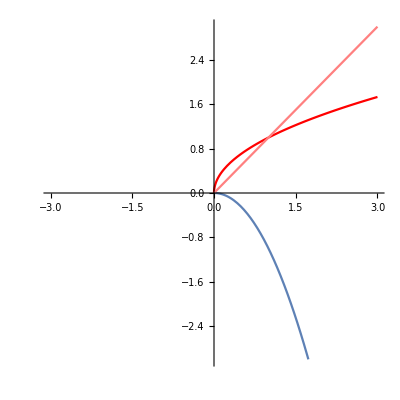

```mathematica
Show[Plot[x^2,{x,0,3},PlotRange->{{-3,3},{-3,3}},AspectRatio->1],Plot[√x,{x,0,3},PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotStyle->Red],
Plot[√(x^2),{x,0,3},PlotRange->{{-3,3},{-3,3}},AspectRatio->1,PlotStyle->Pink]]
```

The geometries of the functions are related in that the inverse function is reflected along the y axis. A function is also flipped along the x axis if it is negative. It can also be said that the -x^2 is the √x but rotated 90 degress clockwise around the origin.

13.	Functions that are their own inverses,i.e.,  f^-1=f or in other words f(f(x))=x which mathematicians write as f^2=I where I is the “identity function. The easiest or “trivial” 		example is, 	of course, f(x)=x (you should say “trivial” with just a hint of contempt in your voice in order to sound “legit” although this doesn’t mean you are actually any 	smarter). One nontrivial example would be f(x)=-x. A nonexample  would be f(x)=x^2 since f(f(x))=(x^2)^2=x^4≠ x. Can you find a different nontrivial example? I will give you a hint: you know one function I am looking for, but there are many. By the way such functions are some times called idempotents.

f(x)=1/x
f(f(x))=1/(1/x)=1/x

14.	Some people call functions with the property f(f(x))=-x or f^2=-I “ericksonpotents”  (and by some people, I am talking about myself). Try to find an example of a real valued, invertible, differentiable  ericksonpotent function or show that they, in fact, don’t exist. You will need to think and use the ideas from the above problems. This problem is particularly interesting if you think about the analogy with solving equations.